```mathematica
SetDirectory["/Users/paul/univ/eratosthenes/results/formatted/"]
benchLaptopPut = Import["out-GET2proc.264466"];
```

/Users/paul/univ/eratosthenes/results/formatted

```mathematica
fit = Fit[benchLaptopPut, {1,x},{x}]
fitPlot=Plot[fit,{x,0,250}];
```

2548.92+87.3835 x

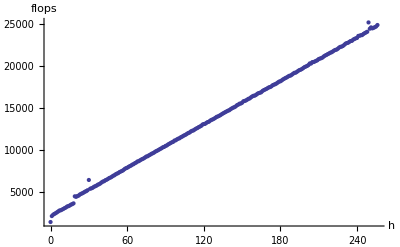

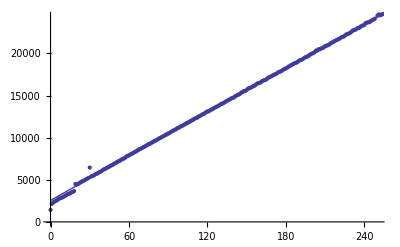

/Users/paul/univ/eratosthenes/report/img

bench-huy-get-p2.pdf

```mathematica
benchlaptopput=ListPlot[benchLaptopPut, AxesLabel->{"h", "flops"}]
both=Show[{fitPlot, benchlaptopput}]
SetDirectory["/Users/paul/univ/eratosthenes/report/img/"]
Export["bench-huy-get-p2.pdf", both]
```

/home/paulvdw/univ/eratosthenes/report/img

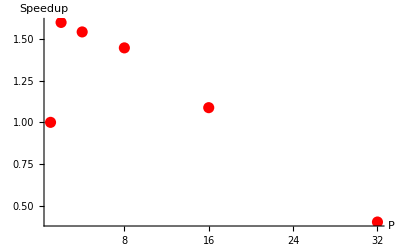

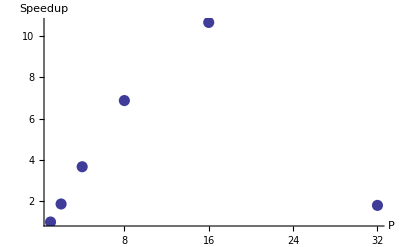

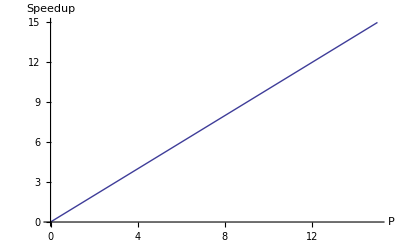

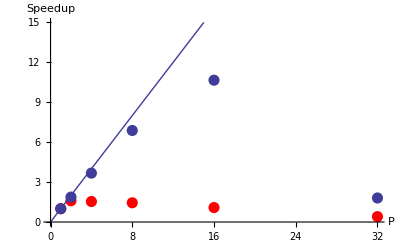

speedup.pdf

```mathematica
SetDirectory["/home/paulvdw/univ/eratosthenes/report/img/"]
speedupHuya= {20.36,10.87,5.54,2.96,1.91,11.28};
speedupHuya = speedupHuya[[1]]/speedupHuya;
speedupMaca = {12.14,7.6,7.88,8.4,11.16,30.04};
speedupMaca = speedupMaca[[1]]/speedupMaca;
P = {1,2,4,8,16,32};
speedupMac = Table[{P[[n]],speedupMaca[[n]]}, {n,1,6}];
speedupHuy = Table[{P[[n]],speedupHuya[[n]]}, {n,1,6}];
a=ListPlot[speedupMac,  PlotStyle->{Red,PointSize[.02]},AxesOrigin->{0,0}, PlotRange->All, AxesLabel->{"P","Speedup"}]
b=ListPlot[speedupHuy,  PlotStyle->PointSize[.02],AxesOrigin->{0,0}, PlotRange->All, AxesLabel->{"P","Speedup"}]
c=Plot[x,{x,0,32}, AxesLabel->{"P","Speedup"}, PlotRange->{All,{0,15}}]
final=Show[{a,b,c}]
Export["speedup.pdf", final]
```

Huygens & 20.36 & 10.87 & 5.54 & 2.96 & 1.91 & 11.28 \\
MacBook & 12.14 & 7.60 & 7.88 & 8.40 & 11.16 & 30.04 \\